```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
$K = 9;
$TrialsFolder = "../../runs/Trials";
$statsDir = "../../runs/Stats-106";
If[!DirectoryQ[$statsDir], CreateDirectory[$statsDir]];
```

```mathematica
Do[Module[{dir, files}, (
Print["N = "<>ToString@$N<>", K = "<>ToString@$K];
dir = $TrialsFolder<>"/N"<>ToString@$N<>"K"<>ToString@$K;
files = FileNames[dir, All];
Print[ToString@Length[files]<>" found. Computing fs."];
changeNK[$N, $K];
Do[Module[{data, cmatdata, simEig, randEig, out, $statFile}, (
Print["Importing "<>ToString[files[[kk]]]];
data = Import[files[[kk]]];
Print["Computing cmatdata"];
cmatdata = Table[(
With[{p = (vv-1)/(Length[data]-1)}, If[Mod[10p, 1]==0, Print[ToString[100p]<>"% done."]]];
cMatOne[data[[vv]]]
), {vv, 1, Length[data]}];

Print["Computing eigenvalues"];
simEig = Flatten[Eigenvalues/@cmatdata[[All, 2]]];
randEig = With[{randMats = (# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[$N], Length[data]]}, Flatten[Eigenvalues/@randMats]];

Print["Computing stats"];
out = {FileBaseName[files[[kk]]], StandardDeviation[simEig], StandardDeviation[randEig], StandardDeviation[simEig]/StandardDeviation[randEig]};

Print["Exporting"];
$statFile = OpenAppend[$statsDir<>"/N"<>ToString[$N]<>"K"<>ToString[$K]<>".dat"];
WriteString[$statFile, StringRiffle[ToString/@out, "    "]<>"\n"];
Close[$statFile];
)], {kk, 1, Length[files]}]
)], {$N, 3, 9}]
```

Syntax::sntxf: "(" cannot be followed by "«1»,«1»)".

```mathematica
data = Import["../../runs/Trials/N5K9/24788149.dat"];
```

```mathematica
changeNK[5, 9];
```

```mathematica
cmatdata = Monitor[Table[cMatOne[data[[kk]]], {kk, 1, Length[data]}], ProgressIndicator[(kk-1)/(Length[data]-1)]];
```

```mathematica
simEig = Flatten[Eigenvalues/@cmatdata[[All, 2]]];
```

```mathematica
randEig = With[{randMats = (# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[$N], 100000]}, Flatten[Eigenvalues/@randMats]];
```

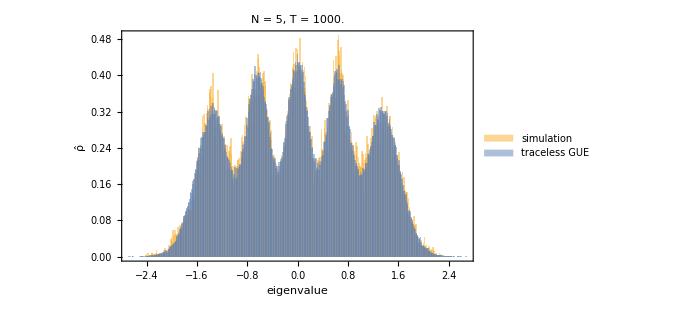

```mathematica
Histogram[{Standardize[simEig], Standardize[randEig]}, 400, PDF,
Frame->True,
FrameStyle->Black,
FrameLabel->{"eigenvalue", "ρ̂"},
ChartLegends->{"simulation", "traceless GUE"},
ImageSize->500,
PlotLabel->Style["N = "<>ToString@$N<>", T = "<>ToString[0.1*Length[data]]]
]
```

```mathematica
Mean[randEig]
```

1.34648×10^-18

```mathematica
Mean[simEig]
```

-3.55271×10^-19

0.208746

```mathematica
StandardDeviation[simEig]/StandardDeviation[randEig]
```

0.0952434